```mathematica
y = Exp[-Exp[ϕ1] t] + Exp[-Exp[ϕ2] t];
ts = {1/3, 1, 3};
MM = ParametricPlot3D[y/.{t->ts},{ϕ1,-10,10},{ϕ2,-10,10}]
```

-Graphics3D-

```mathematica
v = D[y/.{ϕ1->ϕ1 + v1 τ, ϕ2->ϕ2 + v2 τ},τ]/.{τ->0} // Simplify
Avv = D[y/.{ϕ1->ϕ1 + v1 τ, ϕ2->ϕ2 + v2 τ},τ,τ]/.{τ->0} // Simplify
```

-ⅇ^(-ⅇ^ϕ1 t+ϕ1) t v1-ⅇ^(-ⅇ^ϕ2 t+ϕ2) t v2

ⅇ^(-ⅇ^ϕ1 t+ϕ1) t (-1+ⅇ^ϕ1 t) v1^2+ⅇ^(-ⅇ^ϕ2 t+ϕ2) t (-1+ⅇ^ϕ2 t) v2^2

```mathematica
J = Transpose[{ v/.{t->ts,v1->1, v2->0},v/.{t->ts,v1->0, v2->1}}];
J // MatrixForm
```

(-1/3 ⅇ^(-ⅇ^ϕ1/3+ϕ1) | -1/3 ⅇ^(-ⅇ^ϕ2/3+ϕ2)
-ⅇ^(-ⅇ^ϕ1+ϕ1) | -ⅇ^(-ⅇ^ϕ2+ϕ2)
-3 ⅇ^(-3 ⅇ^ϕ1+ϕ1) | -3 ⅇ^(-3 ⅇ^ϕ2+ϕ2))

```mathematica
g = Transpose[J].J // Simplify;
gInv = Inverse[g] // Simplify;
```

```mathematica
a = -gInv.Transpose[J].(Avv/.{t->ts}) // Simplify;
```

```mathematica
eqs = {ϕ1''[s] == (a[[1]]/.{ϕ1->ϕ1[s], v1->ϕ1'[s],ϕ2->ϕ2[s], v2->ϕ2'[s]}),
ϕ2''[s] == (a[[2]]/.{ϕ1->ϕ1[s], v1->ϕ1'[s],ϕ2->ϕ2[s], v2->ϕ2'[s]}),
ϕ1[0] == 0.1, ϕ2[0] == -0.1, ϕ1'[0] == 1, ϕ2'[0] == -1};
sol = NDSolve[eqs,{ϕ1, ϕ2},{s,0,100}]
```

NDSolve::ndsz: At s == 11.7343, step size is effectively zero; singularity or stiff system suspected.

{{ϕ1→InterpolatingFunction[{{0., 11.7343}}, <>],ϕ2→InterpolatingFunction[{{0., 11.7343}}, <>]}}

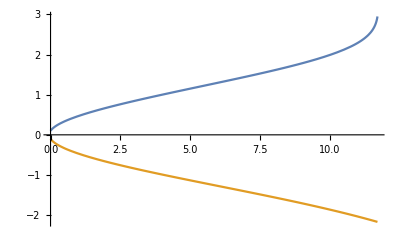

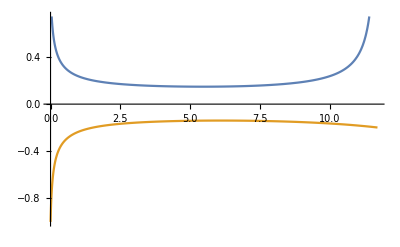

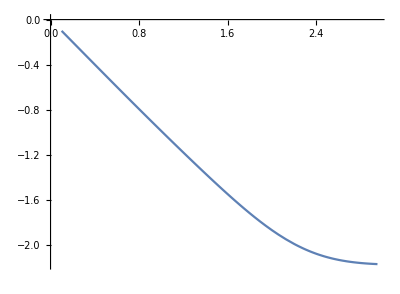

-Graphics3D-

```mathematica
smax = 11.7;
Plot[Evaluate[{ϕ1[s], ϕ2[s]}/.sol],{s,0,smax}]
Plot[Evaluate[{ϕ1'[s], ϕ2'[s]}/.sol],{s,0,smax}]
ParametricPlot[Evaluate[{ϕ1[s],ϕ2[s]}/.sol],{s,0,smax}]
Show[{MM,ParametricPlot3D[Evaluate[y/.{t->ts,ϕ1->ϕ1[s], ϕ2->ϕ2[s]}/.sol],{s,0,smax}]}]
```